```mathematica
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==k*x[t-τ],x[t/;t<=0]==1},
x,{t,-5,10*τ}]
},
Plot[Evaluate[x[t]/.sol],{t,-2,10*τ}]
],
{k,-2,2},
{τ, 0, 4}
]
```

-1.7

{{x→InterpolatingFunction[…]}}

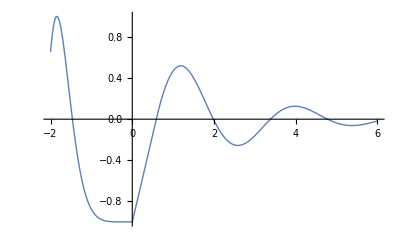

```mathematica
τ:=0.6
k=-1.7
sol=NDSolve[
{x'[t]==k*x[t-τ],x[t/;t<=0]==-Cos[t^3/2]},
x,{t,-5,10*τ}
]

Plot[Evaluate[x[t]/.sol],{t,-2,10*τ},
PlotStyle->{
Thickness->Large,

}
]
```

```mathematica
Manipulate[
ComplexPlot3D[
-ProductLog[τ*z]/τ, {z,-1-1I, 1 + 1I}
],
{τ,1,10}
]
```

```mathematica
r:=1.5
K:=1.2

Needs["MaTeX`"]
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==r*x[t]*(1-x[t-τ]/K),x[t/;t<=0]==0.5},
x,{t,-10,100*τ}]
},
Plot[Evaluate[x[t]/.sol],{t,-10,50*τ},PlotRange->{0,5},
AxesLabel->{MaTeX["t"], MaTeX["x(t)"]},
Epilog->{Gray,Dashed,Line[{{-2,K},{100*τ,K}}],
Text[ MaTeX["x^*_2=K"],{-5.5, K+.0}]
(*{Dashed, Line[{{-10,0.5}, {100,0.5}}]},
{Dashed, Line[{{-10,2*0.5+K}, {100,2*0.5+K}}]}*)

}]
],
{τ, π/(2*r),  π/(2*r)+0.5}
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,104.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -9.99873 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[-9.99873]==r (1-Power[«2»] x[«1»]) x[-9.99873],x[-9.99873/;t≤0]==0.5},x,{-9.99873,-10,104.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: -9.99873 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[-9.99873]==r (1.-1. Power[«2»] x[«1»]) x[-9.99873],x[-9.99873/;t≤0.]==0.5},x,{-9.99873,-10.,104.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: -8.72608 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

```mathematica
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==x[t]-x[t]^3-α*x[t-τ],x[t/;t<=0]==-Sqrt[(1-α)]+0.1},
x,{t,-1,200}]
},
Plot[Evaluate[x[t]/.sol],{t,-1,200},
PlotStyle->{Thickness[0.008]},
PlotRange->{-1.4,1.4},
AxesLabel->{MaTeX["t"],MaTeX["h(t)"]},
Epilog->{
Gray,Dashed,Line[{{-1,Sqrt[(1-α)]},{50,Sqrt[(1-α)]}}],
Line[{{-1,-Sqrt[(1-α)]},{50,-Sqrt[(1-α)]}}]
}
]
],
{α,-1,1},
{τ, 1, 10}
]
```

InterpolatingFunction::dmval: Input value {-3.29085} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{0,5.48881×10^33},{1,0.551853},{2,0.651934},{3,1.14283},{4,1.2226},{5,1.27828},{6,1.29158},{7,1.2975},{8,1.30024},{9,1.30177},{10,1.30246}}

InterpolatingFunction::dmval: Input value {120.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

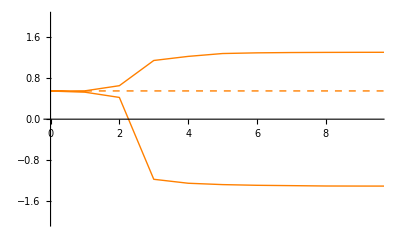

```mathematica
α:=0.7
(*maxs:=Table[
{τ,FindMaximum[
x[t]/.NDSolve[
{x'[t]==r*x[t]*(1-x[t-τ]/K),x[t/;t<=0]==0.5},
x,{t,-10,100*τ}],
{t,50*τ}
]//First},
{τ, .2,1.75,0.1}
]*)
max:=Table[
{τ,FindMaximum[x[t]/.NDSolve[
{x'[t]==x[t]-x[t]^3-α*x[t-τ],x[t/;t<=0]==Sqrt[(1-α)]+0.1},
x,{t,-1,100}],{t,5*τ}]//First
},
{τ,0,10}
]
min:=Table[
{τ,FindMinimum[x[t]/.NDSolve[
{x'[t]==x[t]-x[t]^3-α*x[t-τ],x[t/;t<=0]==Sqrt[(1-α)]+0.1},
x,{t,-1,100}],{t,5*τ}]//First
},
{τ,0,10}
]
max

ListLinePlot[
SortBy[Join[min, max],Last],
PlotStyle->{Orange,Thickness->Large},
Epilog->{
Dashed, Orange, Thickness->Large,
Line[{{1,.55}, {10,.55}}]
},
PlotRange->{{0,9.5},{-2,2}},
AxesLabel->{MaTeX["\\tau"], MaTeX["h"]}]
```

ArcCos[(-2+3 x)/x]/(√(1-(-2+3 x)^2/x^2))

7.79054

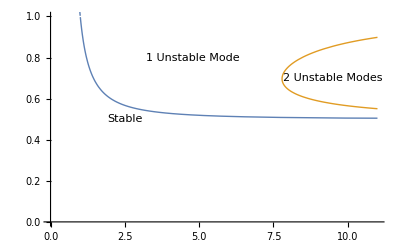

```mathematica
axisFlip=#/. {x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;

t[x_]:=ArcCos[(3x-2)/x]/Sqrt[1-((3x-2)/x)^2]
t2[x_]:=(ArcCos[(3x-2)/x]+2π)/Sqrt[1-((-3x+2)/x)^2]
DisplayForm[t[x]]
t2[.7]
pl:=Plot[
{t[x],t2[x]},
{x,0,10},
PlotStyle->{Thickness->Large},
Epilog->{
Text["Stable",{2.5,0.5}],
Text["1 Unstable Mode",{4.8,0.8}],
Text["2 Unstable Modes",{9.5,0.7}]
},
(*AxesLabel->{Text[MaTeX["\\tau"]], Text[MaTeX["\\alpha"]]},*)
PlotRange->{{0.0,1},{0,11}}]
axisFlip[pl]
```

```mathematica
Solve[
{
b==α*Exp[-a*τ]*Sin[b*τ]
},
α
]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Sin[b τ].

Hold[Solve[{b==α Exp[-a τ] Sin[b τ]},α]]

```mathematica
Plot[{ProductLog[-1,x],ProductLog[x]},{x,-2,5}, PlotRange->{-6,2}, PlotLabels->"Expressions", Epilog->{
Dashed,Line[{{-1/E, 2}, {-1/E, -6}}]
}]
```

-Graphics-

```mathematica
Clear[r,τ]
Solve[l==r*Exp[-l*τ],l]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→ProductLog[r τ]/τ}}

```mathematica
First[{{l->1/2 ProductLog[2 r]}}]
```

{l→1/2 ProductLog[2 r]}

```mathematica
l/.{l->1/2 ProductLog[2 r]}
```

```mathematica
Manipulate[
ComplexPlot3D[1/τ ProductLog[2τ*r],{r,-5-5I,5+5I}, PlotRange->{-5,5}],
{τ,1,5}
]
```

```mathematica
Exp[-b*τ*I]
```

ⅇ^(-ⅈ b τ)

```mathematica
ExpToTrig[ⅇ^(-ⅈ b τ)]
```

```mathematica
Clear[r,α,τ,β]
Solve[
{α+r*Exp[α*τ]Cos[β*τ]==0,
β-r*Exp[-α*τ]Sin[β*τ]==0
},
α
]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is Log[(β Csc[β τ])/r]-InverseFunction[#1 ⅇ^#1&,1,1][-ⅇ^(-α τ) α τ] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-Log[(β Csc[β τ])/r]/τ}}

```mathematica
r=1
Manipulate[
Plot[
-Log[β*Csc[β*τ]/r]/τ,
{τ,-2π,2π},
Epilog->Line[
{
{π/2,5},
{π/2,-5}
}
]
],
{β,-5,5}
]
```

1

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(-h0+h-(-h0+h)^3-α*(-h0+dh))
```

h-(h-h0)^3-h0-(dh-h0) α

```mathematica
Simplify[Expand[h-(h-h0)^3-h0-(dh-h0) α]/.{h0->Sqrt[1-α]}]
```

-h^3+3 h^2 √(1-α)-dh α+h (-2+3 α)

```mathematica
Simplify[h-h^3-√(1-α)+3 h^2 √(1-α)-3 h (1-α)+(1-α)^(3/2)-dh α+√(1-α) α]
```

-h^3+3 h^2 √(1-α)-dh α+h (-2+3 α)

```mathematica
Simplify[h+√(1-α)-(dh+√(1-α)) α]
```

h+(1-α)^(3/2)-dh α

```mathematica
Expand[h+(1-α)^(3/2)-dh α]
```

h+√(1-α)-dh α-√(1-α) α

```mathematica
h+h0-(dh+h0) α
```

h-h^3+h0-3 h^2 h0-3 h h0^2-h0^3-dh α-h0 α

```mathematica
FullSimplify[h-h^3+h0-3 h^2 h0-3 h h0^2-h0^3-dh α-h0 α]/.{h0->Sqrt[1-α]}
```

h-h^3+√(1-α)-3 h^2 √(1-α)-3 h (1-α)-(1-α)^(3/2)-(dh+√(1-α)) α

```mathematica
Simplify[h-h^3+√(1-α)-3 h^2 √(1-α)-3 h (1-α)-(1-α)^(3/2)-(dh+√(1-α)) α]
```

-h^3-3 h^2 √(1-α)-dh α+h (-2+3 α)

```mathematica
Expand[(h+h0)^3]
```

h^3+3 h^2 h0+3 h h0^2+h0^3

```mathematica
Clear[r]
C*Exp[-r*I*t]
```

C ⅇ^(-ⅈ r t)

```mathematica
ExpToTrig[C ⅇ^(-ⅈ r t)]
```

C Cos[r t]-ⅈ C Sin[r t]

```mathematica
ExpToTrig[C ⅇ^(ⅈ r t)]
```

C Cos[r t]+ⅈ C Sin[r t]

C (Cos[(1.5+0. ⅈ) t]+ⅈ Sin[(1.5+0. ⅈ) t])

```mathematica
r:=1.5
K:=1.2
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==r*x[t]*(1-x[t-τ]/K),x[t/;t<=0]==0.5},
x,{t,-10,100*τ}]
},
PolarPlot[Evaluate[x[t]/.sol],{t,0,100*τ},
PlotRange->6,
Epilog->{
Circle[{0,0},K]
},
PolarTicks->None,
PolarGridLines->{{
0, Pi/4,Pi/2,3Pi/4,Pi,5Pi/4,3Pi/2,7Pi/4
},
{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5}
}
]],
{{τ,π/(2*r),0.0}, π/(2*r),  π/(2*r)+0.5,0.001}
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00315755]==r (1-Power[«2»] x[«1»]) x[0.00315755],x[0.00315755/;t≤0]==0.5},x,{0.00315755,-10,154.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00315755 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,135.02}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00275551 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00275551]==r (1-Power[«2»] x[«1»]) x[0.00275551],x[0.00275551/;t≤0]==0.5},x,{0.00275551,-10,135.02}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00275551 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00275551]==r (1-Power[«2»] x[«1»]) x[0.00275551],x[0.00275551/;t≤0]==0.5},x,{0.00275551,-10,135.02}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00275551 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00110939]==r (1-Power[«2»] x[«1»]) x[0.00110939],x[0.00110939/;t≤0]==0.5},x,{0.00110939,-10,108.72}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00110939 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

ReplaceAll::reps: {NDSolve[{x'[t]==r (1-Power[«2»] x[«1»]) x[t],x[t/;t≤0]==0.5},x,{t,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.00112959]==r (1-Power[«2»] x[«1»]) x[0.00112959],x[0.00112959/;t≤0]==0.5},x,{0.00112959,-10,110.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00112959 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

```mathematica
(*τ:=1*)
Clear[τ]
r:=1.5
K:=1.2
(*sol=NDSolve[
{x'[t]==r*x[t]*(1-x[t-τ]/K),x[t/;t<=0]==0.5},
x,{t,-10,100*τ}]*)

(*FindMinimum[x[t]/.sol,{t,1}]*)


maxs:=Table[
{τ,FindMaximum[
x[t]/.NDSolve[
{x'[t]==r*x[t]*(1-x[t-τ]/K),x[t/;t<=0]==0.5},
x,{t,-10,100*τ}],
{t,50*τ}
]//First},
{τ, .2,1.75,0.1}
]
mins:=Table[
{τ,FindMinimum[
x[t]/.NDSolve[
{x'[t]==r*x[t]*(1-x[t-τ]/K),x[t/;t<=0]==0.5},
x,{t,-10,100*τ}],
{t,50*τ}
]//First},
{τ, 0.2,1.75,0.1}
]
together = SortBy[Join[mins,maxs], Last]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum::fmgz will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {395.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum::fmgz will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{{1.7,0.00114343},{1.6,0.00493278},{1.5,0.0166248},{1.4,0.045704},{1.3,0.108241},{1.2,0.236707},{1.1,0.5},{1.,1.09201},{0.9,1.19707},{0.8,1.19993},{0.7,1.2},{0.6,1.2},{0.6,1.2},{0.2,1.2},{0.2,1.2},{0.5,1.2},{0.5,1.2},{0.3,1.2},{0.3,1.2},{0.4,1.2},{0.4,1.2},{0.7,1.2},{0.8,1.20045},{0.9,1.20367},{1.,1.30423},{1.1,2.06772},{1.2,2.75824},{1.3,3.30552},{1.4,3.84313},{1.5,4.43148},{1.6,5.10684},{1.7,5.89144}}

```mathematica
ListLinePlot[
together,
PlotStyle->{Orange,Thickness->Large},
Epilog->{
{Thickness->Large,Orange,Dashed,Line[{{0.5,K},{2.5,K}}]},{Thickness->Large,Orange,Line[{{0,K},{0.5,K}}]},
{
Text["Stable", {0.2,1.3}],
Text["Unstable", {1.5,1.3}],
Text["Limit Cycle", {1.2,3.6}],
Text["Limit Cycle", {0.94,.4}],
Text["Bifurcation", {0.85,1.4}]
}
},
PlotRange->{0,5},
AxesLabel->{MaTeX["\\tau"], MaTeX["x"]}
]
```

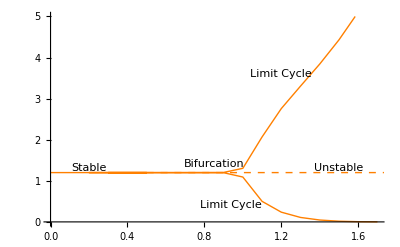

-Graphics-

```mathematica
T:=Sqrt[(1-α)]
T+x+α*(T+xd)
```

x+√(1-α)+(xd+√(1-α)) α

```mathematica
Simplify[x+√(1-α)+(xd+√(1-α)) α]
```

x+xd α+√(1-α) (1+α)

```mathematica
Sin[ArcCos[x]]
```

√(1-x^2)

```mathematica
Needs["MaTeX`"]
Manipulate[
Module[
{sol=NDSolve[
{x'[t]==-b*Tanh[κ*x[t-τ]]+c*Cos[2π*t],x[t/;t<=0]==0.002},
x,{t,-1,5}]
},
Plot[Evaluate[x[t]/.sol],{t,0,mt},
AxesLabel->{
MaTeX["t"],MaTeX["h(t)"]
}
]
],
{κ,0,500},
{τ, 0, 4},
{b, 0, 4},
{c,0,4},
{mt, 0, 10}
]
Reduce[-b*Tanh[κ*x]+c*Cos[2π*t]==0]
```

(Tanh[x κ]==0&&Cos[2 π t]==0)||(Tanh[x κ]≠0&&b==c Cos[2 π t] Coth[x κ])||(Tanh[x κ]==0&&Cos[2 π t]≠0&&c==0)

Plot::plld: Endpoints for t in {t,0,0} must have distinct machine-precision numerical values.